# Data Summary

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Import

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 09:56:53
$MEAS_TIM:
3600 3733
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

\begin{array}{c}
 \text{$\$$SPEC$\_$ID:} \\
 \text{Molnar Range} \\
 \text{$\$$SPEC$\_$REM:} \\
 \text{DET$\#$ 1} \\
 \text{DETDESC$\#$ HPGe Detector 1} \\
 \text{AP$\#$ GammaVision Version 6.07} \\
 \text{$\$$DATE$\_$MEA:} \\
 \text{10/19/2015 09:56:53} \\
 \text{$\$$MEAS$\_$TIM:} \\
 \text{3600 3733} \\
 \text{$\$$DATA:} \\
 \text{0 8191} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{$\$$ROI:} \\
 0 \\
 \text{$\$$PRESETS:} \\
 \text{Live Time} \\
 3600 \\
 0 \\
 \text{$\$$ENER$\_$FIT:} \\
 \text{0.137869 0.366631} \\
 \text{$\$$MCA$\_$CAL:} \\
 3 \\
 \text{1.378689E-001 3.666307E-001 -4.415950E-008 keV} \\
 \text{$\$$SHAPE$\_$CAL:} \\
 3 \\
 \text{2.301834E+000 9.195991E-004 -5.357180E-008} \\
\end{array}

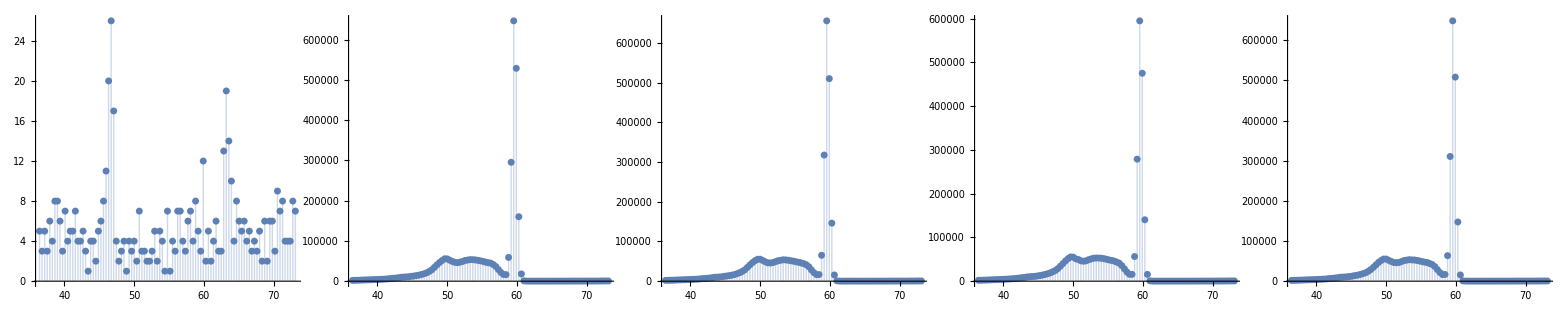

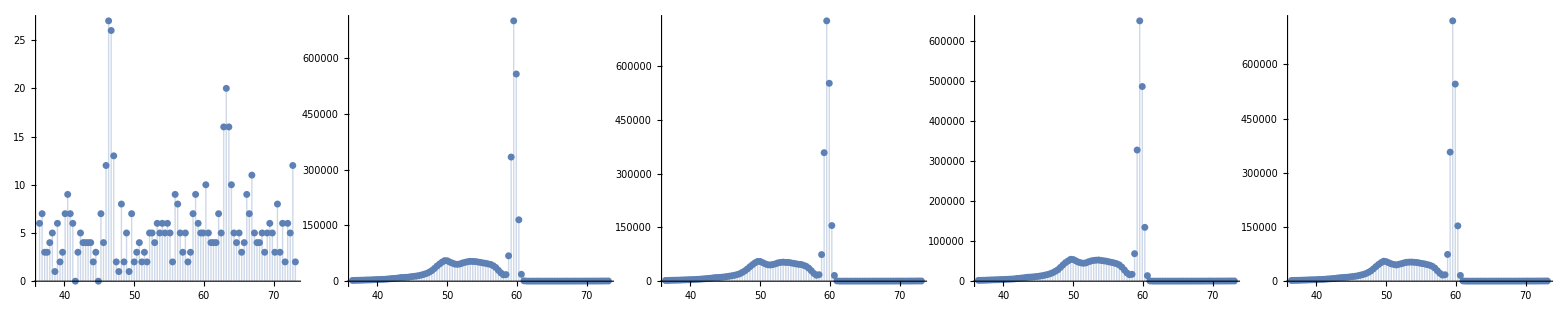

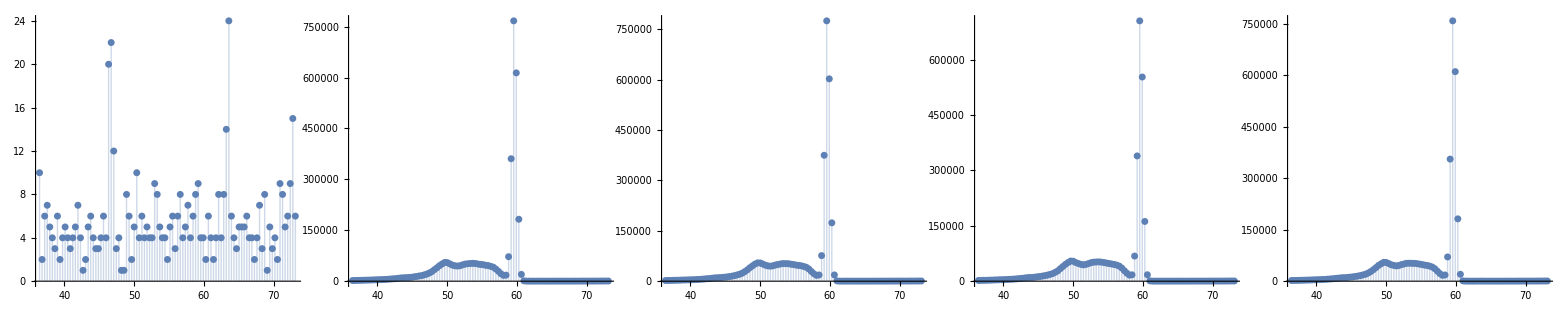

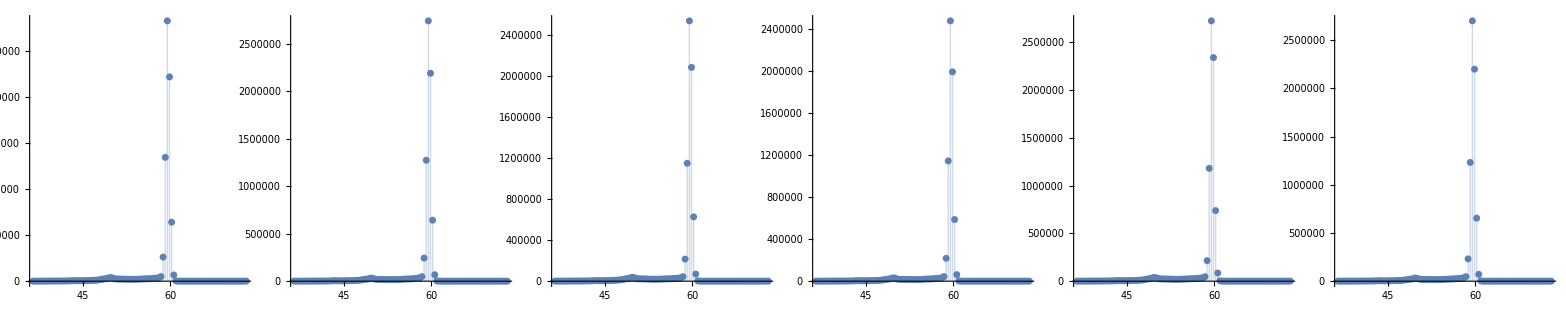

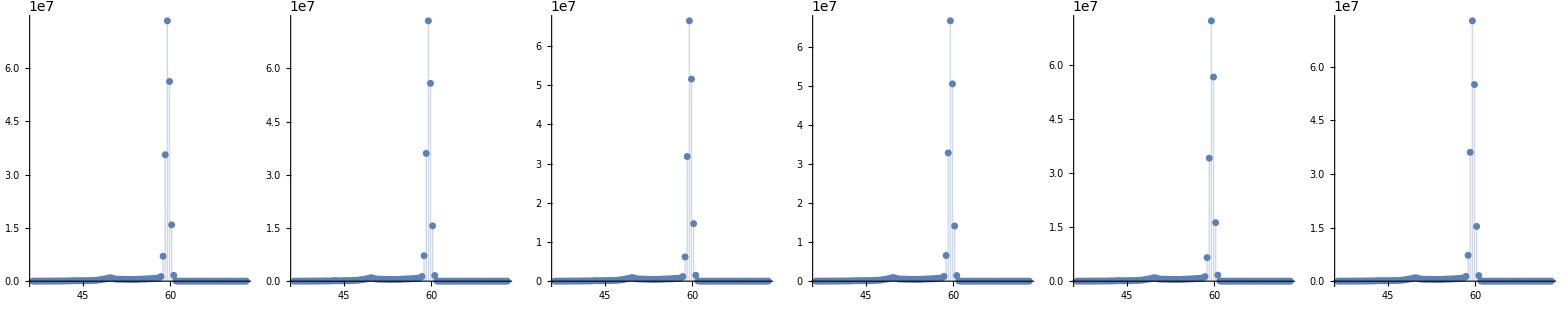

```mathematica
filenames={
{(*    Data Set 1    *)
"Background-10192015.Spe",
"Am-241-1hr-10192015.Spe",
"Am-241-1hrTrial2-10192015.Spe",
"Am-241-ThickFilm-1hr-10192015.Spe",
"Am-241-ThinFilm-1hr-10192015.Spe"},
{(*    Data Set 2    *)
"Background-10232015.Spe",
"Am-241-1hr-10232015.Spe",
"Am-241-1hrTrial2-10232015.Spe",
"Am-241-ThickFilm-1hr-10232015.Spe",
"Am-241-ThinFilm-1hr-10232015.Spe"},
{(*    Data Set 3    *)
"Background-10282015.Spe",
"Am-241-1hr-10282015.Spe",
"Am-241-1hrTrial2-10282015.Spe",
"Am-241-ThickFilm-1hr-10282015.Spe",
"Am-241-ThinFilm-1hr-10282015.Spe"},
{(*    Data Set 4    *)
"Run 1 - Am-241-1hr-NewConfiguration.Spe",
"Run 2 - Am-241-1hr-NewConfiguration.Spe",
"Run 1 - Am-241-1hr-ThickFilm-NewConfiguration.Spe",
"Run 2 - Am-241-1hr-ThickFilm-NewConfiguration.Spe",
"Run 1 - Am-241-1hr-ThinFilm-NewConfiguration.Spe",
"Run 2 - Am-241-1hr-ThinFilm-NewConfiguration.Spe"},
{(*    Data Set 5    *)
"Am-241-24hr-NewConfiguration.Spe",
"Am-241-24hr-NewConfiguration-2.Spe",
"Am-241-24hr-ThickFilm-NewConfiguration.Spe",
"Am-241-24hr-ThickFilm-NewConfiguration-2.Spe",
"Am-241-24hr-ThinFilm-NewConfiguration.Spe",
"Am-241-24hr-ThinFilm-NewConfiguration-2.Spe"}};

For[set=1,set≤3,set++,
numfiles[set]=Length[filenames[[set]]]-1;
For[n=0,n≤numfiles[set],n++,
imported=Import[filenames[[set,n+1]],"Data"];
times=ToExpression[StringSplit[imported[[10]]]];
If[n==1&&set==1,
Print[TableForm[imported[[;;15]]]];
Print[TableForm[imported[[-16;;]]]];
Print[TeXForm[TableForm[Drop[imported,{16,Length[imported]-16}]]]];
];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
energy[set,n]=ToExpression[StringSplit[imported[[-7]]]];
data[set,n]=Table[{i,energy[set,n][[1]]+energy[set,n][[2]](i-1),freq[[i]]},{i,Length[freq]}];
];
Print[Grid[{Table[ListPlot[data[set,i][[100;;200,{2,3}]],ImageSize->Medium,PlotRange->All,Filling->Bottom],{i,0,numfiles[set]}]}]]
]

For[set=4,set≤5,set++,
numfiles[set]=Length[filenames[[set]]];
For[n=1,n≤numfiles[set],n++,
imported=Import[filenames[[set,n]],"Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
energy[set,n]=ToExpression[StringSplit[imported[[-7]]]];
data[set,n]=Table[{i,energy[set,n][[1]]+energy[set,n][[2]](i-1),freq[[i]]},{i,Length[freq]}];
];
Print[Grid[{Table[ListPlot[data[set,i][[100;;200,{2,3}]],ImageSize->Medium,PlotRange->All,Filling->Bottom],{i,1,numfiles[set]}]}]];
]

Clear[set,n,imported,times,deadtime,freq]
```

## Analysis

## Physical Measurements

### Thickness

```mathematica
thickrawdata=Import["Thickness.xlsx","Data"];
For[set=1,set≤Length[thickrawdata],set++,
thickdata=thickrawdata[[set,All,2]]-thickrawdata[[set,All,1]];
Print["Thickness Set "<>ToString[set]<>" = ",thickset[set]={Mean[thickdata],StandardDeviation[thickdata]}];
]
thickweights=WeightedData@@Transpose[Table[{thickset[set][[1]],1/(thickset[set][[2]])^2},{set,Length[thickrawdata]}]];
thick={Mean[thickweights],StandardDeviation[thickweights]};
Print["Thickness Summary (mm) = ",{thick[[1]],thick[[2]],100*thick[[2]]/thick[[1]]}]
```

Thickness Set 1 = {0.887356,0.00593745}

Thickness Set 2 = {0.884844,0.00637965}

Thickness Set 3 = {0.884719,0.00859699}

Thickness Summary (mm) = {0.885891,0.00158212,0.17859}

### Area

```mathematica
areaformula[areadata_]:=Sum[(1/2)*(areadata[[k+1,1]]+areadata[[k,1]])*(areadata[[k+1,2]]-areadata[[k,2]]),{k,Length[areadata]-1}];
frontareadata=Import["Area.xlsx",{"Data",1}];
backareadata=Import["Area.xlsx",{"Data",2}];
trials=5000;delta=0.5*10^-3;
montefrontarea=Table[areaformula[Table[{frontareadata[[i,1]]+RandomReal[{-delta,delta}],frontareadata[[i,2]]+RandomReal[{-delta,delta}]},{i,Length[frontareadata]}]],{i,1,trials}]/100;
montebackarea=Table[areaformula[Table[{backareadata[[i,1]]+RandomReal[{-delta,delta}],backareadata[[i,2]]+RandomReal[{-delta,delta}]},{i,Length[backareadata]}]],{i,1,trials}]/100;
areafront={Mean[montefrontarea],StandardDeviation[montefrontarea]};
Print["Front Area (cm^2) = ",{areafront[[1]],areafront[[2]],100*areafront[[2]]/areafront[[1]]}]
areaback={Mean[montebackarea],StandardDeviation[montebackarea]};
Print["Front Area (cm^2) = ",{areaback[[1]],areaback[[2]],100*areaback[[2]]/areaback[[1]]}]
areaweight=WeightedData@@{{areafront[[1]],areaback[[1]]},1/({areafront[[2]],areaback[[2]]})^2};
area={Mean[areaweight],StandardDeviation[areaweight]};
Print["Area (cm^2) = ",{area[[1]],area[[2]],100*area[[2]]/area[[1]]}]
```

Front Area (cm^2) = {6.17081,0.0000391921,0.000635121}

Front Area (cm^2) = {6.17065,0.0000386328,0.000626073}

Area (cm^2) = {6.17073,0.000112281,0.00181957}

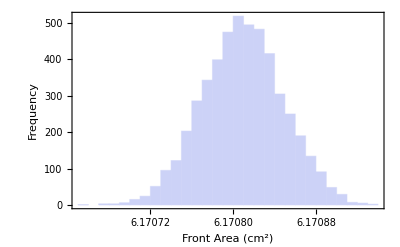

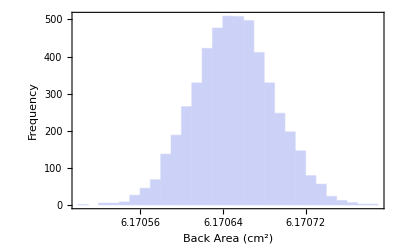

```mathematica
imagesize=400;
imagedpi=300;
fontsize=12;
Histogram[montefrontarea,PlotTheme->"Classic",ImageSize->imagesize,
FrameLabel->{"Front Area (cm^2)","Frequency"},
PlotTheme->"Classic",
Frame->{{True,False},{True,False}},
Axes->True,
BaseStyle->{FontSize->fontsize},ImageSize->imagesize]
Export["../Thesis/Draft/Figures/frontarea.png",%,ImageResolution->imagedpi];
Histogram[montebackarea,PlotTheme->"Classic",ImageSize->imagesize,
FrameLabel->{"Back Area (cm^2)","Frequency"},
PlotTheme->"Classic",
Frame->{{True,False},{True,False}},
Axes->True,
BaseStyle->{FontSize->fontsize},ImageSize->imagesize]
Export["../Thesis/Draft/Figures/backarea.png",%,ImageResolution->imagedpi];
```

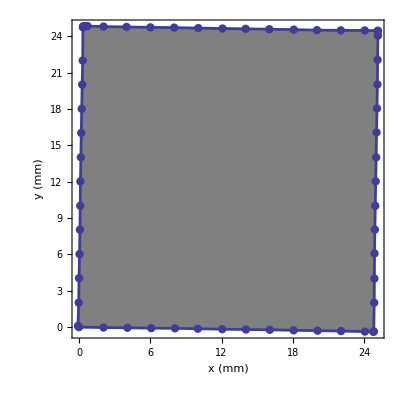

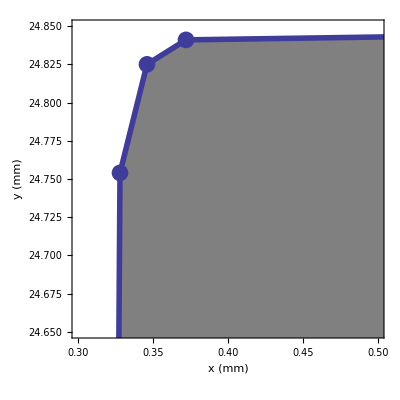

```mathematica
Show[Graphics[{Gray,Polygon[frontareadata]}],ListPlot[frontareadata,PlotTheme->"Classic",PlotStyle->{PointSize[0.015]}],ListLinePlot[frontareadata,PlotStyle->Thickness[0.005],PlotTheme->"Classic"],Axes->True,AspectRatio->1,Frame->True,FrameLabel->{"x (mm)","y (mm)"},BaseStyle->{FontFamily->"Times",FontSize->13}]
Export["../Thesis/Draft/Figures/frontpolygon.png",%,ImageResolution->imagedpi];
Show[Graphics[{Gray,Polygon[frontareadata]},PlotRangeClipping->True,PlotRange->{{0.3,0.5},{24.65,24.85}},Frame->True],ListLinePlot[frontareadata,PlotStyle->Thickness[0.01],PlotTheme->"Classic"],ListPlot[frontareadata,PlotTheme->"Classic",PlotRange->{{0.3,0.5},{24.65,24.85}},PlotStyle->{PointSize[0.03]}],PlotRange->{{0.3,0.5},{24.65,24.85}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"x (mm)","y (mm)"},BaseStyle->{FontSize->12,FontFamily->"Times"}]
Export["../Thesis/Draft/Figures/cornerzoom.png",%,ImageResolution->imagedpi];
```

### Mass

```mathematica
massdata=Import["Mass.xlsx",{"Data",1}][[All,1]];
mass={Mean[massdata],StandardDeviation[massdata]};
Print["Mass (g) = ",{mass[[1]],mass[[2]],100*mass[[2]]/mass[[1]]}]
```

Mass (g) = {1.53548,0.000139841,0.00910733}

## Fitting

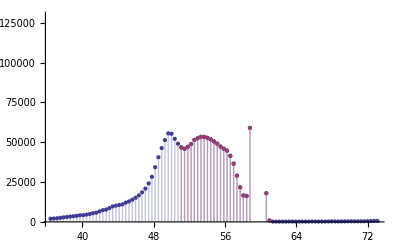

```mathematica
ListPlot[{data[1,1][[100;;200,{2,3}]],data[1,1][[140;;167,{2,3}]]},PlotTheme->"Classic",Filling->Bottom]
```

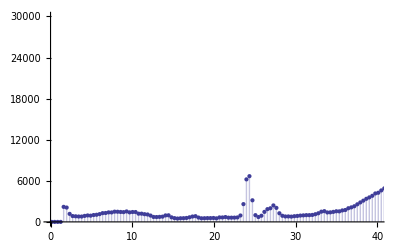

```mathematica
ListPlot[data[1,1][[All,{2,3}]],PlotTheme->"Classic",Filling->Bottom,PlotRange->{{0,40},{0,30000}}]
```

```mathematica
(*    Parameters    *)
symbol={"μ","σ","p","A","P","B"};
titlesize=24;



(*    Data Set Parameters    *)
mu={
{24.2,48.4,49.7,53.2,56.0,59.6},
{24.2,48.4,49.7,53.2,56.0,59.6},
{24.2,48.4,49.7,53.2,56.0,59.6},
{24.1,26.4,51.6,49.6,56.7,58.6,59.6},
{24.1,26.4,51.6,49.6,56.7,58.6,59.6}
};
sigma={
{0.4,5.4,1.4,1.3,1.5,0.4},
{0.4,5.4,1.4,1.3,1.5,0.4},
{0.4,5.4,1.4,1.3,1.5,0.4},
{0.6,0.4,4.0,0.7,1.4,0.8,0.36},
{0.6,0.4,4.0,0.7,1.4,0.8,0.36}
};
p={
{6000,15000,30000,30000,30000,730000},
{6000,15000,30000,30000,30000,730000},
{6000,15000,30000,30000,30000,730000},
{5000,20000,18000,18000,16000,24000,2400000},
{20000,50000,180000,180000,160000,240000,29000000}
};
npeaks=Table[Length[mu[[i]]],{i,Length[mu]}];
region={
{1,500},
{1,500},
{1,500},
{1,200},
{1,200}
};
cmu={59.6,59.6,59.6,59.6,59.6};
csigma={0.4,0.4,0.4,0.4,0.4};
cp={730000,730000,730000,730000,70000000};
cregion={
{142,167,160},(*154*)
{142,167,160},
{142,167,160},
{140,167,160},
{140,167,160}
};
cparamnames={a,b,c,d};
intensities={
Table[{i,{4}},{i,Tuples[{{1,2},{3}}]}],
Table[{i,{4}},{i,Tuples[{{1,2},{3}}]}],
Table[{i,{4}},{i,Tuples[{{1,2},{3}}]}],
Table[{i,{5,6}},{i,Tuples[{{1,2},{3,4}}]}],
Table[{i,{5,6}},{i,Tuples[{{1,2},{3,4}}]}]
};
runnames={
{"Source 1","Source 2","Thick","Thin"},
{"Source 1","Source 2","Thick","Thin"},
{"Source 1","Source 2","Thick","Thin"},
{"Source 1","Source 2","Thick 1","Thick 2","Thin 1","Thin 2"},
{"Source 1","Source 2","Thick 1","Thick 2","Thin 1","Thin 2"}
};



(*    Equations    *)
F[x_,params__]:=Total[List[params][[2*Length[List[params]]/3+1;;]]*Exp[-1/2((x-List[params][[;;Length[List[params]]/3]])/(List[params][[Length[List[params]]/3+1;;2*Length[List[params]]/3]]))^2]];
cubicbkg[x_,a_,b_,c_,d_]:=a x^3+b x^2+c x+d;
GaussArea[a_,sigma_]:=a*sigma*Sqrt[2*π];
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];
coeff[initial_,intensity1_,area_,mass_]:=(Log[initial]-Log[intensity1])*area/mass;
measurement[initial_,intensity1_,intensity2_,thick_]:=(Log[intensity2]-Log[initial])/(Log[intensity1]-Log[initial])*thick;

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}



(* Fitting and Calculations *)
For[set=1,set≤Length[filenames],set++,
Print[Text[Style["Data Set ",FontSize->titlesize]],Text[Style[set,FontSize->titlesize]]];
For[run=1,run≤numfiles[set],run++,

(*    Model Fitting    *)
model[set,run]=NonlinearModelFit[data[set,run][[region[[set,1]];;region[[set,2]],{2,3}]],
F@@Join[{x},Flatten[Transpose[Table[{Symbol["mu"<>ToString[i]],Symbol["sigma"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,npeaks[[set]]}]]]],
Join[
Table[{Symbol["mu"<>ToString[i]],mu[[set,i]]},{i,npeaks[[set]]}],
Table[{Symbol["sigma"<>ToString[i]],sigma[[set,i]]},{i,npeaks[[set]]}],
Table[{Symbol["p"<>ToString[i]],p[[set,i]]},{i,npeaks[[set]]}]
],x];


params[set,run]=model[set,run]["BestFitParameters"][[All,2]];
paramerrors[set,run]=model[set,run]["ParameterErrors"];

(*    Intensity Calculations    *)
peakdata=Table[err@@Join[{F},{{j,0}},
{{params[set,run][[npeaks[[set]]]],paramerrors[set,run][[npeaks[[set]]]]}},
{{params[set,run][[2npeaks[[set]]]],paramerrors[set,run][[2npeaks[[set]]]]}},
{{params[set,run][[3npeaks[[set]]]],paramerrors[set,run][[3npeaks[[set]]]]}}],{j,Table[data[set,run][[i[[1]],2]],{i,Position[data[set,run][[;;200,2]],_?(params[set,run][[npeaks[[set]]]]-2*fwhm[params[set,run][[2npeaks[[set]]]]]<#<params[set,run][[npeaks[[set]]]]+2*fwhm[params[set,run][[2npeaks[[set]]]]]&)]}]}];
bkgdata=Table[err@@Join[{F},{{j,0}},
Table[{params[set,run][[l]],paramerrors[set,run][[l]]},{l,0*npeaks[[set]]+1,npeaks[[set]]-1}],Table[{params[set,run][[l]],paramerrors[set,run][[l]]},{l,1*npeaks[[set]]+1,2*npeaks[[set]]-1}],Table[{params[set,run][[l]],paramerrors[set,run][[l]]},{l,2*npeaks[[set]]+1,3*npeaks[[set]]-1}]],
{j,Table[data[set,run][[i[[1]],2]],{i,Position[data[set,run][[;;200,2]],_?(params[set,run][[npeaks[[set]]]]-2*fwhm[params[set,run][[2npeaks[[set]]]]]<#<params[set,run][[npeaks[[set]]]]+2*fwhm[params[set,run][[2npeaks[[set]]]]]&)]}]}];
gaussarea[set,run]=err[GaussArea,{params[set,run][[2npeaks[[set]]]],paramerrors[set,run][[2npeaks[[set]]]]},{params[set,run][[3npeaks[[set]]]],paramerrors[set,run][[3npeaks[[set]]]]}];
peak[set,run]={Total[peakdata[[All,1]]*energy[set,run][[2]]],Sqrt[Total[(peakdata[[All,2]]*energy[set,run][[2]])^2]]};
bkg[set,run]={Total[bkgdata[[All,1]]*energy[set,run][[2]]],Sqrt[Total[(bkgdata[[All,2]]*energy[set,run][[2]])^2]]};
intensity[set,run]={peak[set,run][[1]],peak[set,run][[2]]};
(*intensity[set,run]={gaussarea[set,run][[1]],Sqrt[gaussarea[set,run][[1]]+2*bkg[set,run][[1]]]};*)

(*    Model Fitting    *)
cubicprelim[set,run]=NonlinearModelFit[data[set,run][[Join[Table[i,{i,cregion[[set,1]],cregion[[set,3]]}],{cregion[[set,2]]}],{2,3}]],cubicbkg[x,a,b,c,d],cparamnames,x];
cmodel[set,run]=NonlinearModelFit[data[set,run][[cregion[[set,1]];;cregion[[set,2]],{2,3}]],cubicbkg[x,a,b,c,d]+F[x,mu1,sigma1,p1],Join[Table[{cparamnames[[i]],cubicprelim[set,run]["BestFitParameters"][[i,2]]},{i,1,4}],{{mu1,cmu[[set]]},{sigma1,csigma[[set]]},{p1,cp[[set]]}}],x];
cparams[set,run]=cmodel[set,run]["BestFitParameters"][[All,2]];
cparamerrors[set,run]=cmodel[set,run]["ParameterErrors"];

(*    Intensity Calculations    *)
cpeakdata=Table[err@@Join[{F},{{j,0}},
{{cparams[set,run][[-3]],cparamerrors[set,run][[-3]]}},
{{cparams[set,run][[-2]],cparamerrors[set,run][[-2]]}},
{{cparams[set,run][[-1]],cparamerrors[set,run][[-1]]}}],{j,Table[data[set,run][[i[[1]],2]],{i,Position[data[set,run][[;;200,2]],_?(cparams[set,run][[-3]]-2*fwhm[cparams[set,run][[-2]]]<#<cparams[set,run][[-3]]+2*fwhm[cparams[set,run][[-2]]]&)]}]}];
cbkgdata=Table[err@@Join[{cubicbkg},{{j,0}},
Table[{cparams[set,run][[l]],cparamerrors[set,run][[l]]},{l,4}]],
{j,Table[data[set,run][[i[[1]],2]],{i,Position[data[set,run][[;;200,2]],_?(cparams[set,run][[-3]]-2*fwhm[cparams[set,run][[-2]]]<#<cparams[set,run][[-3]]+2*fwhm[cparams[set,run][[-2]]]&)]}]}];
cgaussarea[set,run]=err[GaussArea,{cparams[set,run][[-2]],cparamerrors[set,run][[-2]]},{cparams[set,run][[-1]],cparamerrors[set,run][[-1]]}];


cpeak[set,run]={Total[cpeakdata[[All,1]]*energy[set,run][[2]]],Sqrt[Total[(cpeakdata[[All,2]]*energy[set,run][[2]])^2]]};
cbkg[set,run]={Total[cbkgdata[[All,1]]*energy[set,run][[2]]],Sqrt[Total[(cbkgdata[[All,2]]*energy[set,run][[2]])^2]]};
cintensity[set,run]={cpeak[set,run][[1]],cpeak[set,run][[2]]};
(*cintensity[set,run]={cgaussarea[set,run][[1]],Sqrt[cgaussarea[set,run][[1]]+2*cbkg[set,run][[1]]]};*)

(*    Trial Summary    *)
Print[runnames[[set,run]]];
Print[TableForm[Insert[Insert[Insert[Insert[
Table[{symbol[[i/npeaks[[set]]]],params[set,run][[i]],paramerrors[set,run][[i]],100*paramerrors[set,run][[i]]/params[set,run][[i]],cparams[set,run][[-4+i/npeaks[[set]]]],cparamerrors[set,run][[-4+i/npeaks[[set]]]],100*cparamerrors[set,run][[-4+i/npeaks[[set]]]]/cparams[set,run][[-4+i/npeaks[[set]]]]},{i,{npeaks[[set]],2npeaks[[set]],3npeaks[[set]]}}],
Join[{symbol[[4]]},gaussarea[set,run],{100*gaussarea[set,run][[2]]/gaussarea[set,run][[1]]},cgaussarea[set,run],{100*cgaussarea[set,run][[2]]/cgaussarea[set,run][[1]]}],4],
Join[{symbol[[5]]},peak[set,run],{100*bkg[set,run][[2]]/peak[set,run][[1]]},cpeak[set,run],{100*cbkg[set,run][[2]]/cpeak[set,run][[1]]}],5],
Join[{symbol[[6]]},bkg[set,run],{100*bkg[set,run][[2]]/bkg[set,run][[1]]},cbkg[set,run],{100*cbkg[set,run][[2]]/cbkg[set,run][[1]]}],6]
,{{},{"Gaussian Value"},{"Error"},{"Percent Error"},{"Cubic Value"},{"Error"},{"Percent Error"}},1]]];

];

(*    Data Set Summary    *)
Print[""];
Print["Gaussian Model Summary"];
Print[TableForm[Insert[Table[Join[{runnames[[set,i]]},intensity[set,i],{100*intensity[set,i][[2]]/intensity[set,i][[1]]}],{i,1,numfiles[set]}],{{},{"Intensity"},{"Error"},{"Percent Error"}},1]]];

For[trial=1,trial≤Length[intensities[[set]]],trial++,
initial=intensity[set,intensities[[set,trial,1,1]]];
intensity1=intensity[set,intensities[[set,trial,1,2]]];

Print["\nTrial "<>ToString[trial]<>" ",intensities[[set,trial]]];
atten[set,trial]=err[coeff,initial,intensity1,area,mass];
Print["attenuation coefficient = ",Join[atten[set,trial],{100*atten[set,trial][[2]]/atten[set,trial][[1]]}]];

For[i=1,i≤Length[intensities[[set,trial,2]]],i++,
intensity2=intensity[set,intensities[[set,trial,2,i]]];
thin[set,trial,i]=err[measurement,initial,intensity1,intensity2,thick];Print["thin foil measurement = ",Join[thin[set,trial,i],{100*thin[set,trial,i][[2]]/thin[set,trial,i][[1]]}]];
];
];

(*    Data Set Summary    *)
Print[""];
Print["Cubic Model Summary"];
Print[TableForm[Insert[Table[Join[{runnames[[set,trial]]},cintensity[set,trial],{100*cintensity[set,trial][[2]]/cintensity[set,trial][[1]]}],{trial,numfiles[set]}],{{},{"Intensity"},{"Error"},{"Percent Error"}},1]]];

For[trial=1,trial≤Length[intensities[[set]]],trial++,
cinitial=cintensity[set,intensities[[set,trial,1,1]]];
cintensity1=cintensity[set,intensities[[set,trial,1,2]]];

Print["\nTrial "<>ToString[trial]<>" ",intensities[[set,trial]]];
catten[set,trial]=err[coeff,cinitial,cintensity1,area,mass];
Print["attenuation coefficient = ",Join[catten[set,trial],{100*catten[set,trial][[2]]/catten[set,trial][[1]]}]];

For[i=1,i≤Length[intensities[[set,trial,2]]],i++,
cintensity2=cintensity[set,intensities[[set,trial,2,i]]];
cthin[set,trial,i]=err[measurement,cinitial,cintensity1,cintensity2,thick];Print["thin foil measurement = ",Join[cthin[set,trial,i],{100*cthin[set,trial,i][[2]]/cthin[set,trial,i][[1]]}]];
];
];

Print[""];
];
Clear[set,run,trial,initial,intensity1,intensity2]
```

Data Set 1

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Source 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6414 | 0.000460945 | 0.00077286 | 59.6434 | 0.00157026 | 0.00263276
σ | 0.367201 | 0.000514477 | 0.140108 | 0.365712 | 0.00180046 | 0.492316
p | 671576. | 748.955 | 0.111522 | 669696. | 2574.7 | 0.384457
A | 618143. | 1106.93 | 0.179073 | 613913. | 3834.78 | 0.624646
P | 618143. | 613.756 | 0.313447 | 613913. | 2118.91 | 5541.29
B | 20911.4 | 1937.55 | 9.26555 | 26389. | 3.40187×10^7 | 128912.

Source 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6216 | 0.000460758 | 0.000772803 | 59.6236 | 0.00155158 | 0.00260229
σ | 0.36809 | 0.000512744 | 0.139299 | 0.36671 | 0.00177098 | 0.482936
p | 671878. | 747.26 | 0.11122 | 670088. | 2539.71 | 0.379011
A | 619918. | 1105.02 | 0.178252 | 615949. | 3781.33 | 0.613903
P | 619914. | 612.659 | 0.288587 | 615946. | 2089.63 | 5169.58
B | 20055.7 | 1788.99 | 8.92012 | 25800.1 | 3.18418×10^7 | 123418.

Thick

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6325 | 0.000484081 | 0.000811775 | 59.6346 | 0.00173242 | 0.00290505
σ | 0.367304 | 0.000538232 | 0.146536 | 0.365814 | 0.00198205 | 0.54182
p | 613824. | 717.963 | 0.116966 | 612209. | 2596.48 | 0.424117
A | 565145. | 1059.61 | 0.187493 | 561371. | 3862.64 | 0.688073
P | 565141. | 588.043 | 0.30803 | 561368. | 2135.48 | 5780.19
B | 19359.8 | 1740.81 | 8.99185 | 25153. | 3.24481×10^7 | 129003.

Thin

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6251 | 0.000461958 | 0.000774772 | 59.6271 | 0.0015696 | 0.00263236
σ | 0.367846 | 0.000514763 | 0.13994 | 0.366424 | 0.00179285 | 0.489284
p | 665615. | 743.113 | 0.111643 | 663779. | 2546.79 | 0.383681
A | 613732. | 1098.69 | 0.179018 | 609674. | 3790.83 | 0.621779
P | 613728. | 609.125 | 0.29685 | 609671. | 2095.18 | 5231.95
B | 20175.5 | 1821.85 | 9.03002 | 26051.4 | 3.18977×10^7 | 122441.

Gaussian Model Summary

| Intensity | Error | Percent Error
Source 1 | 618143. | 613.756 | 0.0992904
Source 2 | 619914. | 612.659 | 0.0988296
Thick | 565141. | 588.043 | 0.104052
Thin | 613728. | 609.125 | 0.0992499

Trial 1 {{1,3},{4}}

attenuation coefficient = {0.360257,0.00578006,1.60443}

thin foil measurement = {0.0708269,0.0133564,18.8578}

Trial 2 {{2,3},{4}}

attenuation coefficient = {0.371757,0.0057673,1.55136}

thin foil measurement = {0.0960404,0.0127572,13.2832}

Cubic Model Summary

| Intensity | Error | Percent Error
Source 1 | 613913. | 2118.91 | 0.345148
Source 2 | 615946. | 2089.63 | 0.339256
Thick | 561368. | 2135.48 | 0.380406
Thin | 609671. | 2095.18 | 0.343658

Trial 1 {{1,3},{4}}

attenuation coefficient = {0.359585,0.0206424,5.7406}

thin foil measurement = {0.0686493,0.0464759,67.7004}

Trial 2 {{2,3},{4}}

attenuation coefficient = {0.37287,0.020484,5.4936}

thin foil measurement = {0.0977666,0.0438544,44.8563}

Data Set 2

Source 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6296 | 0.000437608 | 0.000733877 | 59.6315 | 0.00144773 | 0.0024278
σ | 0.369496 | 0.000489089 | 0.132367 | 0.368138 | 0.00165656 | 0.449984
p | 720759. | 760.263 | 0.105481 | 718817. | 2531.85 | 0.352225
A | 667559. | 1129.87 | 0.169255 | 663315. | 3790.47 | 0.571443
P | 667558. | 624.543 | 0.276621 | 663314. | 2089.15 | 5069.66
B | 21594.2 | 1846.61 | 8.55141 | 26751. | 3.36278×10^7 | 125706.

Source 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6136 | 0.0004276 | 0.000717285 | 59.6154 | 0.00143259 | 0.00240305
σ | 0.367913 | 0.000475948 | 0.129364 | 0.36654 | 0.00163179 | 0.445188
p | 740035. | 765.05 | 0.10338 | 737990. | 2584.17 | 0.350163
A | 682476. | 1130.16 | 0.165598 | 678049. | 3840.46 | 0.566398
P | 682473. | 626.847 | 0.256773 | 678046. | 2124.17 | 4785.24
B | 20679. | 1752.4 | 8.47433 | 26898.3 | 3.24461×10^7 | 120625.

Thick

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.607 | 0.000456077 | 0.000765139 | 59.609 | 0.00156625 | 0.00262753
σ | 0.368336 | 0.000505896 | 0.137346 | 0.366997 | 0.00178183 | 0.485518
p | 661862. | 727.588 | 0.109931 | 660177. | 2524.65 | 0.38242
A | 611085. | 1075.04 | 0.175923 | 607313. | 3753.43 | 0.618039
P | 611082. | 596.465 | 0.278018 | 607310. | 2075.61 | 5228.94
B | 19432.2 | 1698.92 | 8.7428 | 24926.3 | 3.17559×10^7 | 127399.

Thin

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6122 | 0.000428397 | 0.00071864 | 59.6139 | 0.00141275 | 0.00236984
σ | 0.368085 | 0.000477365 | 0.129689 | 0.366706 | 0.00160879 | 0.438714
p | 733900. | 760.187 | 0.103582 | 731882. | 2526.26 | 0.345172
A | 677134. | 1123.89 | 0.165977 | 672743. | 3755.41 | 0.558224
P | 677131. | 623.101 | 0.305249 | 672739. | 2076.85 | 4717.16
B | 20612. | 2066.94 | 10.0279 | 26815.6 | 3.17342×10^7 | 118342.

Gaussian Model Summary

| Intensity | Error | Percent Error
Source 1 | 667558. | 624.543 | 0.0935563
Source 2 | 682473. | 626.847 | 0.0918495
Thick | 611082. | 596.465 | 0.0976081
Thin | 677131. | 623.101 | 0.0920207

Trial 1 {{1,3},{4}}

attenuation coefficient = {0.355244,0.00543363,1.52955}

thin foil measurement = {-0.142686,0.0143563,-10.0615}

Trial 2 {{2,3},{4}}

attenuation coefficient = {0.444041,0.00538645,1.21305}

thin foil measurement = {0.0630035,0.0100771,15.9946}

Cubic Model Summary

| Intensity | Error | Percent Error
Source 1 | 663314. | 2089.15 | 0.314956
Source 2 | 678046. | 2124.17 | 0.313279
Thick | 607310. | 2075.61 | 0.341771
Thin | 672739. | 2076.85 | 0.308715

Trial 1 {{1,3},{4}}

attenuation coefficient = {0.354493,0.0186778,5.26887}

thin foil measurement = {-0.141696,0.0483494,-34.122}

Trial 2 {{2,3},{4}}

attenuation coefficient = {0.442769,0.0186321,4.20809}

thin foil measurement = {0.063178,0.0341655,54.0782}

Data Set 3

Source 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6325 | 0.000408891 | 0.000685684 | 59.6341 | 0.00126632 | 0.00212349
σ | 0.368443 | 0.000458629 | 0.124477 | 0.367241 | 0.0014494 | 0.394673
p | 792058. | 784.999 | 0.0991088 | 790109. | 2439.99 | 0.308817
A | 731505. | 1163.93 | 0.159114 | 727324. | 3644.87 | 0.501134
P | 731505. | 643.728 | 0.260029 | 727319. | 2011.07 | 4199.87
B | 21935. | 1902.12 | 8.67165 | 27511.7 | 3.05465×10^7 | 111031.

Source 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6218 | 0.000404432 | 0.00067833 | 59.6234 | 0.00127015 | 0.0021303
σ | 0.368333 | 0.000453085 | 0.12301 | 0.367001 | 0.00144986 | 0.395058
p | 794114. | 778.588 | 0.0980448 | 791936. | 2455.21 | 0.310026
A | 733184. | 1153.32 | 0.157303 | 728529. | 3658.54 | 0.502182
P | 733179. | 638.303 | 0.271342 | 728525. | 2020.96 | 4226.95
B | 21456.5 | 1989.43 | 9.27188 | 27910.3 | 3.07944×10^7 | 110333.

Thick

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6249 | 0.000424326 | 0.00071166 | 59.6267 | 0.00142415 | 0.00238844
σ | 0.368918 | 0.000472402 | 0.128051 | 0.36755 | 0.00162734 | 0.442753
p | 724615. | 740.335 | 0.102169 | 722699. | 2508.31 | 0.347075
A | 670081. | 1097.7 | 0.163816 | 665831. | 3745.8 | 0.562575
P | 670077. | 607.817 | 0.272841 | 665827. | 2067. | 4724.89
B | 19720.2 | 1828.25 | 9.27093 | 25859.5 | 3.14596×10^7 | 121656.

Thin

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6342 | 0.000409659 | 0.000686952 | 59.6359 | 0.00128401 | 0.00215309
σ | 0.368403 | 0.000460059 | 0.124879 | 0.367214 | 0.00147026 | 0.400381
p | 784802. | 779.997 | 0.0993878 | 782863. | 2451.46 | 0.313141
A | 724726. | 1156.68 | 0.159602 | 720602. | 3662.77 | 0.508293
P | 724725. | 639.554 | 0.270221 | 720602. | 2020.76 | 4509.62
B | 21929.6 | 1958.36 | 8.9302 | 26698.7 | 3.24964×10^7 | 121715.

Gaussian Model Summary

| Intensity | Error | Percent Error
Source 1 | 731505. | 643.728 | 0.0880006
Source 2 | 733179. | 638.303 | 0.0870596
Thick | 670077. | 607.817 | 0.0907084
Thin | 724725. | 639.554 | 0.0882478

Trial 1 {{1,3},{4}}

attenuation coefficient = {0.35249,0.00507905,1.4409}

thin foil measurement = {0.094044,0.0119806,12.7393}

Trial 2 {{2,3},{4}}

attenuation coefficient = {0.361679,0.0050528,1.39704}

thin foil measurement = {0.11416,0.0115133,10.0852}

Cubic Model Summary

| Intensity | Error | Percent Error
Source 1 | 727319. | 2011.07 | 0.276504
Source 2 | 728525. | 2020.96 | 0.277405
Thick | 665827. | 2067. | 0.310441
Thin | 720602. | 2020.76 | 0.280426

Trial 1 {{1,3},{4}}

attenuation coefficient = {0.355002,0.0167071,4.7062}

thin foil measurement = {0.0930606,0.0376496,40.4571}

Trial 2 {{2,3},{4}}

attenuation coefficient = {0.361657,0.0167312,4.62626}

thin foil measurement = {0.10765,0.0367613,34.149}

Data Set 4

Source 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6266 | 0.000305763 | 0.000512797 | 59.6256 | 0.000444329 | 0.000745199
σ | 0.366736 | 0.000549524 | 0.149842 | 0.366587 | 0.000504601 | 0.137648
p | 2.90504×10^6 | 7378.66 | 0.253995 | 2.89735×10^6 | 3125.71 | 0.107882
A | 2.67052×10^6 | 7875.36 | 0.2949 | 2.66236×10^6 | 4656.13 | 0.174887
P | 2.6705×10^6 | 4130.31 | 0.3973 | 2.66235×10^6 | 2576.31 | 1107.49
B | 61209.4 | 10609.9 | 17.3338 | 64096.1 | 2.94853×10^7 | 46001.8

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Source 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6338 | 0.000194557 | 0.000326253 | 59.6328 | 0.000457302 | 0.000766864
σ | 0.365779 | 0.000367174 | 0.100381 | 0.365645 | 0.000520155 | 0.142257
p | 2.83578×10^6 | 4785.09 | 0.16874 | 2.82838×10^6 | 3148.6 | 0.111322
A | 2.60005×10^6 | 5104.95 | 0.19634 | 2.59232×10^6 | 4682.66 | 0.180636
P | 2.60003×10^6 | 2674.9 | 0.25967 | 2.5923×10^6 | 2592.93 | 1143.11
B | 59904.4 | 6751.52 | 11.2705 | 62504.5 | 2.96329×10^7 | 47409.2

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Thick 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6437 | 0.000310223 | 0.000520126 | 59.6427 | 0.000450861 | 0.000755937
σ | 0.365785 | 0.000572231 | 0.156439 | 0.36572 | 0.000514278 | 0.140621
p | 2.64429×10^6 | 7310.69 | 0.276471 | 2.6377×10^6 | 2894.43 | 0.109733
A | 2.42451×10^6 | 7701.77 | 0.317662 | 2.41805×10^6 | 4313.04 | 0.178369
P | 2.42451×10^6 | 4042.59 | 0.409751 | 2.41803×10^6 | 2385.97 | 1124.81
B | 57783.8 | 9934.47 | 17.1925 | 58880.8 | 2.71982×10^7 | 46191.9

Thick 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6361 | 0.000297273 | 0.000498479 | 59.635 | 0.00047828 | 0.000802013
σ | 0.36568 | 0.00055117 | 0.150725 | 0.365642 | 0.000544355 | 0.148876
p | 2.56942×10^6 | 6827.1 | 0.265706 | 2.56295×10^6 | 2984.05 | 0.11643
A | 2.35519×10^6 | 7194.61 | 0.305479 | 2.34902×10^6 | 4439.59 | 0.188998
P | 2.35517×10^6 | 3776.47 | 0.380483 | 2.349×10^6 | 2457.87 | 1195.13
B | 55666.6 | 8961.03 | 16.0977 | 56801.8 | 2.80737×10^7 | 49424.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

Thin 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6603 | 0.000303573 | 0.000508836 | 59.6593 | 0.000434454 | 0.000728224
σ | 0.365971 | 0.000555789 | 0.151867 | 0.365838 | 0.000497814 | 0.136075
p | 2.88027×10^6 | 7407.78 | 0.25719 | 2.87272×10^6 | 3036.41 | 0.105698
A | 2.64222×10^6 | 7891.83 | 0.298681 | 2.63435×10^6 | 4539.07 | 0.172303
P | 2.64222×10^6 | 4137.94 | 0.408067 | 2.63435×10^6 | 2507.21 | 1144.38
B | 62704.4 | 10782. | 17.1951 | 61036.5 | 3.01468×10^7 | 49391.5

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Thin 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6407 | 0.00020788 | 0.000348554 | 59.6396 | 0.000479062 | 0.000803262
σ | 0.36549 | 0.00039088 | 0.106947 | 0.365438 | 0.000545921 | 0.149388
p | 2.80723×10^6 | 5243.26 | 0.186777 | 2.80028×10^6 | 3267.58 | 0.116688
A | 2.57183×10^6 | 5535.32 | 0.215228 | 2.56511×10^6 | 4862.4 | 0.189559
P | 2.57182×10^6 | 2904.01 | 0.278754 | 2.56509×10^6 | 2691.65 | 1197.23
B | 60183.8 | 7169.04 | 11.9119 | 61567.1 | 3.071×10^7 | 49880.5

Gaussian Model Summary

| Intensity | Error | Percent Error
Source 1 | 2.6705×10^6 | 4130.31 | 0.154664
Source 2 | 2.60003×10^6 | 2674.9 | 0.102879
Thick 1 | 2.42451×10^6 | 4042.59 | 0.166738
Thick 2 | 2.35517×10^6 | 3776.47 | 0.160348
Thin 1 | 2.64222×10^6 | 4137.94 | 0.156608
Thin 2 | 2.57182×10^6 | 2904.01 | 0.112917

Trial 1 {{1,3},{5,6}}

attenuation coefficient = {0.388354,0.00913979,2.35347}

thin foil measurement = {0.097587,0.0191877,19.6622}

thin foil measurement = {0.345176,0.0147614,4.27648}

Trial 2 {{1,4},{5,6}}

attenuation coefficient = {0.504965,0.00895326,1.77305}

thin foil measurement = {0.0750513,0.0149151,19.8732}

thin foil measurement = {0.265465,0.0115499,4.35081}

Trial 3 {{2,3},{5,6}}

attenuation coefficient = {0.280885,0.00787372,2.80319}

thin foil measurement = {-0.204025,0.025985,-12.7362}

thin foil measurement = {0.138294,0.0183541,13.2718}

Trial 4 {{2,4},{5,6}}

attenuation coefficient = {0.397496,0.0076564,1.92616}

thin foil measurement = {-0.144171,0.0178064,-12.3508}

thin foil measurement = {0.0977237,0.013116,13.4215}

Cubic Model Summary

| Intensity | Error | Percent Error
Source 1 | 2.66235×10^6 | 2576.31 | 0.0967682
Source 2 | 2.5923×10^6 | 2592.93 | 0.100024
Thick 1 | 2.41803×10^6 | 2385.97 | 0.098674
Thick 2 | 2.349×10^6 | 2457.87 | 0.104635
Thin 1 | 2.63435×10^6 | 2507.21 | 0.0951739
Thin 2 | 2.56509×10^6 | 2691.65 | 0.104934

Trial 1 {{1,3},{5,6}}

attenuation coefficient = {0.386827,0.00555425,1.43585}

thin foil measurement = {0.0973131,0.0118576,12.185}

thin foil measurement = {0.342495,0.011654,3.40267}

Trial 2 {{1,4},{5,6}}

attenuation coefficient = {0.503217,0.00572781,1.13824}

thin foil measurement = {0.0748054,0.00922153,12.3274}

thin foil measurement = {0.263279,0.00912836,3.46719}

Trial 3 {{2,3},{5,6}}

attenuation coefficient = {0.279678,0.00564658,2.01896}

thin foil measurement = {-0.204802,0.0200272,-9.77881}

thin foil measurement = {0.134312,0.0172858,12.8698}

Trial 4 {{2,4},{5,6}}

attenuation coefficient = {0.396068,0.00581737,1.46878}

thin foil measurement = {-0.144618,0.0136014,-9.40503}

thin foil measurement = {0.094843,0.0124285,13.1042}

Data Set 5

Source 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6183 | 0.000307458 | 0.00051571 | 59.6173 | 0.00043828 | 0.000735156
σ | 0.36654 | 0.000541957 | 0.147857 | 0.366395 | 0.000496574 | 0.13553
p | 7.49903×10^7 | 191943. | 0.255957 | 7.47938×10^7 | 79630.4 | 0.106467
A | 6.88996×10^7 | 203663. | 0.295594 | 6.86918×10^7 | 118388. | 0.172347
P | 6.88992×10^7 | 106981. | 0.38503 | 6.86914×10^7 | 65569.3 | 1094.8
B | 1.54454×10^6 | 265283. | 17.1755 | 1.6195×10^6 | 7.52037×10^8 | 46436.3

Source 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6147 | 0.000316472 | 0.000530862 | 59.6137 | 0.000449928 | 0.000754739
σ | 0.366783 | 0.000554674 | 0.151227 | 0.36667 | 0.000509357 | 0.138914
p | 7.49345×10^7 | 199957. | 0.266842 | 7.47402×10^7 | 81626.4 | 0.109213
A | 6.8894×10^7 | 211308. | 0.306715 | 6.86942×10^7 | 121386. | 0.176705
P | 6.88937×10^7 | 111027. | 0.386634 | 6.86938×10^7 | 67222.4 | 1123.25
B | 1.55214×10^6 | 266366. | 17.1612 | 1.61555×10^6 | 7.71604×10^8 | 47761.1

Thick 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6229 | 0.000315244 | 0.00052873 | 59.6219 | 0.000453868 | 0.000761244
σ | 0.366042 | 0.000541127 | 0.147832 | 0.365944 | 0.000514759 | 0.140666
p | 6.81346×10^7 | 176850. | 0.25956 | 6.79579×10^7 | 75019.1 | 0.110391
A | 6.25156×10^7 | 186738. | 0.298706 | 6.23368×10^7 | 111464. | 0.17881
P | 6.25152×10^7 | 98281.5 | 0.381133 | 6.23365×10^7 | 61751.8 | 1135.08
B | 1.41783×10^6 | 238266. | 16.805 | 1.46913×10^6 | 7.0757×10^8 | 48162.4

Thick 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6137 | 0.00031363 | 0.000526105 | 59.6126 | 0.000455374 | 0.000763888
σ | 0.367019 | 0.000548164 | 0.149356 | 0.366925 | 0.000515446 | 0.140477
p | 6.80396×10^7 | 180234. | 0.264896 | 6.78647×10^7 | 74962.6 | 0.110459
A | 6.25951×10^7 | 190352. | 0.3041 | 6.24183×10^7 | 111544. | 0.178704
P | 6.25948×10^7 | 100005. | 0.387527 | 6.2418×10^7 | 61753.8 | 1135.82
B | 1.4231×10^6 | 242572. | 17.0453 | 1.47362×10^6 | 7.08954×10^8 | 48109.8

Thin 1

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6269 | 0.0002999 | 0.000502961 | 59.626 | 0.000430817 | 0.000722532
σ | 0.365495 | 0.000521784 | 0.142761 | 0.365316 | 0.000489024 | 0.133863
p | 7.44337×10^7 | 179024. | 0.240515 | 7.42347×10^7 | 77921.5 | 0.104966
A | 6.81931×10^7 | 190732. | 0.279693 | 6.79776×10^7 | 115637. | 0.17011
P | 6.81927×10^7 | 100327. | 0.381706 | 6.79773×10^7 | 64099.5 | 1079.63
B | 1.51508×10^6 | 260296. | 17.1803 | 1.59988×10^6 | 7.33903×10^8 | 45872.5

Thin 2

| Gaussian Value | Error | Percent Error | Cubic Value | Error | Percent Error
μ | 59.6122 | 0.000312439 | 0.000524119 | 59.6112 | 0.000447018 | 0.00074989
σ | 0.367166 | 0.000550004 | 0.149797 | 0.367044 | 0.000505829 | 0.137812
p | 7.42027×10^7 | 195278. | 0.263168 | 7.40101×10^7 | 80224.9 | 0.108397
A | 6.82924×10^7 | 206799. | 0.302814 | 6.80924×10^7 | 119389. | 0.175334
P | 6.82921×10^7 | 108578. | 0.386907 | 6.80921×10^7 | 66093.4 | 1114.69
B | 1.53391×10^6 | 264227. | 17.2257 | 1.59993×10^6 | 7.59014×10^8 | 47440.3

Gaussian Model Summary

| Intensity | Error | Percent Error
Source 1 | 6.88992×10^7 | 106981. | 0.155272
Source 2 | 6.88937×10^7 | 111027. | 0.161157
Thick 1 | 6.25152×10^7 | 98281.5 | 0.157212
Thick 2 | 6.25948×10^7 | 100005. | 0.159765
Thin 1 | 6.81927×10^7 | 100327. | 0.147123
Thin 2 | 6.82921×10^7 | 108578. | 0.158991

Trial 1 {{1,3},{5,6}}

attenuation coefficient = {0.390762,0.00888007,2.2725}

thin foil measurement = {0.0939057,0.018492,19.6921}

thin foil measurement = {0.0806409,0.0194139,24.0745}

Trial 2 {{1,4},{5,6}}

attenuation coefficient = {0.385652,0.00895336,2.32162}

thin foil measurement = {0.0951499,0.0187271,19.6816}

thin foil measurement = {0.0817093,0.0196624,24.0638}

Trial 3 {{2,3},{5,6}}

attenuation coefficient = {0.390439,0.00904783,2.31735}

thin foil measurement = {0.0932507,0.0188454,20.2094}

thin foil measurement = {0.079975,0.0197632,24.7117}

Trial 4 {{2,4},{5,6}}

attenuation coefficient = {0.385329,0.00911977,2.36675}

thin foil measurement = {0.0944873,0.0190845,20.1979}

thin foil measurement = {0.0810355,0.0200158,24.7}

Cubic Model Summary

| Intensity | Error | Percent Error
Source 1 | 6.86914×10^7 | 65569.3 | 0.0954549
Source 2 | 6.86938×10^7 | 67222.4 | 0.0978579
Thick 1 | 6.23365×10^7 | 61751.8 | 0.099062
Thick 2 | 6.2418×10^7 | 61753.8 | 0.098936
Thin 1 | 6.79773×10^7 | 64099.5 | 0.0942954
Thin 2 | 6.80921×10^7 | 66093.4 | 0.0970647

Trial 1 {{1,3},{5,6}}

attenuation coefficient = {0.390128,0.00552865,1.41714}

thin foil measurement = {0.0953702,0.0116381,12.2031}

thin foil measurement = {0.0799656,0.0119141,14.8991}

Trial 2 {{1,4},{5,6}}

attenuation coefficient = {0.384881,0.005525,1.43551}

thin foil measurement = {0.0966703,0.0117891,12.1952}

thin foil measurement = {0.0810558,0.01207,14.891}

Trial 3 {{2,3},{5,6}}

attenuation coefficient = {0.39027,0.00559608,1.4339}

thin foil measurement = {0.0956575,0.0117637,12.2977}

thin foil measurement = {0.0802585,0.0120416,15.0035}

Trial 4 {{2,4},{5,6}}

attenuation coefficient = {0.385023,0.00559248,1.4525}

thin foil measurement = {0.0969611,0.011916,12.2895}

thin foil measurement = {0.0813523,0.0121989,14.9951}

```mathematica
model[1,1]["ParameterTable"]
model[4,1]["ParameterTable"]
cmodel[1,1]["ParameterTable"]
cmodel[4,1]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 24.1827 | 0.0456001 | 530.32 | 5.86447101651×10^-669
mu2 | 48.4062 | 0.37578 | 128.815 | 1.51197577415×10^-375
mu3 | 49.7478 | 0.0691448 | 719.473 | 9.91282247914×10^-733
mu4 | 53.1597 | 0.114225 | 465.396 | 1.12638791278×10^-641
mu5 | 56.0496 | 0.175334 | 319.673 | 2.59976258048×10^-563
mu6 | 59.6414 | 0.000460945 | 129390. | 1.73455427613×10^-1819
sigma1 | 0.434644 | 0.0456135 | 9.52885 | 7.78579×10^-20
sigma2 | 5.39483 | 0.173201 | 31.1478 | 1.6382×10^-117
sigma3 | 1.36285 | 0.0535368 | 25.4564 | 3.16224×10^-91
sigma4 | 1.29711 | 0.12291 | 10.5534 | 1.45186×10^-23
sigma5 | 1.46633 | 0.0993891 | 14.7534 | 6.42726×10^-41
sigma6 | 0.367201 | 0.000514477 | 713.737 | 4.6821242391×10^-731
p1 | 6954.54 | 631.956 | 11.0048 | 2.78539×10^-25
p2 | 15044.6 | 731.997 | 20.5527 | 7.14722×10^-68
p3 | 38689.2 | 1319.22 | 29.3273 | 2.98712×10^-109
p4 | 36574.8 | 3032.92 | 12.0593 | 1.89×10^-29
p5 | 37243.2 | 2715.49 | 13.7151 | 2.22761×10^-36
p6 | 671576. | 748.955 | 896.685 | 8.70127063882×10^-779

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 24.1012 | 0.349945 | 68.8714 | 9.21295×10^-131
mu2 | 26.4198 | 0.123372 | 214.147 | 1.14073×10^-217
mu3 | 51.5677 | 0.322141 | 160.078 | 3.63878×10^-195
mu4 | 49.5875 | 0.0440197 | 1126.48 | 1.38386969940595×10^-346
mu5 | 56.7179 | 0.859015 | 66.0267 | 1.31825×10^-127
mu6 | 58.545 | 0.162217 | 360.905 | 3.79198×10^-258
mu7 | 59.6266 | 0.000305763 | 195009. | 3.05821263813711×10^-747
sigma1 | 0.60377 | 0.358358 | 1.68482 | 0.0937652
sigma2 | 0.429125 | 0.125302 | 3.42474 | 0.000763044
sigma3 | 4.0738 | 0.227503 | 17.9066 | 9.33334×10^-42
sigma4 | 0.666241 | 0.053194 | 12.5247 | 2.99011×10^-26
sigma5 | 1.37607 | 0.516411 | 2.66467 | 0.00841051
sigma6 | 0.787719 | 0.27802 | 2.83332 | 0.00513554
sigma7 | 0.366736 | 0.000549524 | 667.37 | 6.73175×10^-306
p1 | 2101.32 | 1053.1 | 1.99537 | 0.0475194
p2 | 5042.11 | 1244.82 | 4.05047 | 0.0000760522
p3 | 21538.1 | 702.883 | 30.6425 | 4.05841×10^-73
p4 | 18173.4 | 1164.31 | 15.6087 | 3.15924×10^-35
p5 | 16278.5 | 5017.28 | 3.24448 | 0.00140414
p6 | 24523.1 | 11666.9 | 2.10194 | 0.0369576
p7 | 2.90504×10^6 | 7378.66 | 393.708 | 6.67371×10^-265

| Estimate | Standard Error | t-Statistic | P-Value
a | 242.079 | 33.4701 | 7.23268 | 7.24475×10^-7
b | -41760.8 | 5669.19 | -7.36629 | 5.58285×10^-7
c | 2.39047×10^6 | 319653. | 7.47835 | 4.49508×10^-7
d | -4.5375×10^7 | 5.99972×10^6 | -7.56286 | 3.82168×10^-7
mu1 | 59.6434 | 0.00157026 | 37983. | 2.47065×10^-76
sigma1 | 0.365712 | 0.00180046 | 203.122 | 3.59607×10^-33
p1 | 669696. | 2574.7 | 260.107 | 3.28113×10^-35

| Estimate | Standard Error | t-Statistic | P-Value
a | -288.274 | 31.0265 | -9.2912 | 6.90776×10^-9
b | 47820.1 | 5220.78 | 9.15956 | 8.80686×10^-9
c | -2.63963×10^6 | 292383. | -9.02799 | 1.12511×10^-8
d | 4.85092×10^7 | 5.44979×10^6 | 8.90111 | 1.42781×10^-8
mu1 | 59.6256 | 0.000444329 | 134192. | 2.73326×10^-95
sigma1 | 0.366587 | 0.000504601 | 726.489 | 1.07891×10^-47
p1 | 2.89735×10^6 | 3125.71 | 926.94 | 6.46807×10^-50

## Summary

### Attenuation Coefficient

```mathematica
For[set=1,set≤Length[filenames],set++,
attencoeffs[set]=Table[Join[atten[set,i],{100*atten[set,i][[2]]/atten[set,i][[1]]}],{i,Length[intensities[[set]]]}];
attendata[set]=WeightedData[attencoeffs[set][[All,1]],1/(attencoeffs[set][[All,2]])^2];
Print[{Mean[attendata[set]],StandardDeviation[attendata[set]],100*StandardDeviation[attendata[set]]/Mean[attendata[set]]}];
];
```

{0.36602,0.00813177,2.22168}

{0.400029,0.0627891,15.6961}

{0.357108,0.00649705,1.81935}

{0.386222,0.0912516,23.6267}

{0.388069,0.00295616,0.761763}

```mathematica
For[set=1,set≤Length[filenames],set++,
cattencoeffs[set]=Table[Join[catten[set,i],{100*catten[set,i][[2]]/catten[set,i][[1]]}],{i,Length[intensities[[set]]]}];
cattendata[set]=WeightedData[cattencoeffs[set][[All,1]],1/(cattencoeffs[set][[All,2]])^2];
Print[{Mean[cattendata[set]],StandardDeviation[cattendata[set]],100*StandardDeviation[cattendata[set]]/Mean[cattendata[set]]}];
];
```

{0.366279,0.00939384,2.56467}

{0.398739,0.062421,15.6546}

{0.358324,0.00470573,1.31326}

{0.390543,0.0913048,23.3789}

{0.387573,0.0030306,0.781943}

```mathematica
finalattendata=WeightedData[{Mean[cattendata[5]],Mean[attendata[5]]},1/({StandardDeviation[cattendata[5]],StandardDeviation[attendata[5]]})^2];
Print["Final Attenuation Coefficient (cm^2/g) : ",{Mean[finalattendata],StandardDeviation[finalattendata],100*StandardDeviation[finalattendata]/Mean[finalattendata]}]
```

Final Attenuation Coefficient (cm^2/g) : {0.387827,0.000350532,0.0903835}

### Thin Foil Thickness

```mathematica
For[i=1,i≤Length[filenames],i++,
For[j=1,j≤Length[intensities[[i]]],j++,
For[k=1,k≤Length[intensities[[i,j,2]]],k++,
Print["Set "<>ToString[i]<>" Trial "<>ToString[intensities[[i,j,1]]]<>" Thin "<>ToString[k]<>" ",Join[thin[i,j,k],{100*thin[i,j,k][[2]]/thin[i,j,k][[1]]}]];
];
];
]
```

Set 1 Trial {1, 3} Thin 1 {0.0708269,0.0133564,18.8578}

Set 1 Trial {2, 3} Thin 1 {0.0960404,0.0127572,13.2832}

Set 2 Trial {1, 3} Thin 1 {-0.142686,0.0143563,-10.0615}

Set 2 Trial {2, 3} Thin 1 {0.0630035,0.0100771,15.9946}

Set 3 Trial {1, 3} Thin 1 {0.094044,0.0119806,12.7393}

Set 3 Trial {2, 3} Thin 1 {0.11416,0.0115133,10.0852}

Set 4 Trial {1, 3} Thin 1 {0.097587,0.0191877,19.6622}

Set 4 Trial {1, 3} Thin 2 {0.345176,0.0147614,4.27648}

Set 4 Trial {1, 4} Thin 1 {0.0750513,0.0149151,19.8732}

Set 4 Trial {1, 4} Thin 2 {0.265465,0.0115499,4.35081}

Set 4 Trial {2, 3} Thin 1 {-0.204025,0.025985,-12.7362}

Set 4 Trial {2, 3} Thin 2 {0.138294,0.0183541,13.2718}

Set 4 Trial {2, 4} Thin 1 {-0.144171,0.0178064,-12.3508}

Set 4 Trial {2, 4} Thin 2 {0.0977237,0.013116,13.4215}

Set 5 Trial {1, 3} Thin 1 {0.0939057,0.018492,19.6921}

Set 5 Trial {1, 3} Thin 2 {0.0806409,0.0194139,24.0745}

Set 5 Trial {1, 4} Thin 1 {0.0951499,0.0187271,19.6816}

Set 5 Trial {1, 4} Thin 2 {0.0817093,0.0196624,24.0638}

Set 5 Trial {2, 3} Thin 1 {0.0932507,0.0188454,20.2094}

Set 5 Trial {2, 3} Thin 2 {0.079975,0.0197632,24.7117}

Set 5 Trial {2, 4} Thin 1 {0.0944873,0.0190845,20.1979}

Set 5 Trial {2, 4} Thin 2 {0.0810355,0.0200158,24.7}

```mathematica
For[i=1,i≤Length[filenames],i++,
For[j=1,j≤Length[intensities[[i]]],j++,
For[k=1,k≤Length[intensities[[i,j,2]]],k++,
Print["Set "<>ToString[i]<>" Source "<>ToString[intensities[[i,j,1,1]]]<>" Thin "<>ToString[k]<>" ",Join[cthin[i,j,k],{100*cthin[i,j,k][[2]]/cthin[i,j,k][[1]]}]];
];
];
]
```

Set 1 Source 1 Thin 1 {0.0686493,0.0464759,67.7004}

Set 1 Source 2 Thin 1 {0.0977666,0.0438544,44.8563}

Set 2 Source 1 Thin 1 {-0.141696,0.0483494,-34.122}

Set 2 Source 2 Thin 1 {0.063178,0.0341655,54.0782}

Set 3 Source 1 Thin 1 {0.0930606,0.0376496,40.4571}

Set 3 Source 2 Thin 1 {0.10765,0.0367613,34.149}

Set 4 Source 1 Thin 1 {0.0973131,0.0118576,12.185}

Set 4 Source 1 Thin 2 {0.342495,0.011654,3.40267}

Set 4 Source 1 Thin 1 {0.0748054,0.00922153,12.3274}

Set 4 Source 1 Thin 2 {0.263279,0.00912836,3.46719}

Set 4 Source 2 Thin 1 {-0.204802,0.0200272,-9.77881}

Set 4 Source 2 Thin 2 {0.134312,0.0172858,12.8698}

Set 4 Source 2 Thin 1 {-0.144618,0.0136014,-9.40503}

Set 4 Source 2 Thin 2 {0.094843,0.0124285,13.1042}

Set 5 Source 1 Thin 1 {0.0953702,0.0116381,12.2031}

Set 5 Source 1 Thin 2 {0.0799656,0.0119141,14.8991}

Set 5 Source 1 Thin 1 {0.0966703,0.0117891,12.1952}

Set 5 Source 1 Thin 2 {0.0810558,0.01207,14.891}

Set 5 Source 2 Thin 1 {0.0956575,0.0117637,12.2977}

Set 5 Source 2 Thin 2 {0.0802585,0.0120416,15.0035}

Set 5 Source 2 Thin 1 {0.0969611,0.011916,12.2895}

Set 5 Source 2 Thin 2 {0.0813523,0.0121989,14.9951}

```mathematica
For[j=1,j≤Length[intensities[[5]]],j++,
For[k=1,k≤Length[intensities[[5,j,2]]],k++,
Print[thin[5,j,k]];
];
]
```

{0.0939057,0.018492}

{0.0806409,0.0194139}

{0.0951499,0.0187271}

{0.0817093,0.0196624}

{0.0932507,0.0188454}

{0.079975,0.0197632}

{0.0944873,0.0190845}

{0.0810355,0.0200158}

```mathematica
thin5trial1data=WeightedData@@Transpose[Table[{thin[5,j,1][[1]],1/(thin[5,j,1][[2]])^2},{j,Length[intensities[[5]]]}]];
thin5trial1={Mean[thin5trial1data],StandardDeviation[thin5trial1data]};
thin5trial2data=WeightedData@@Transpose[Table[{thin[5,j,2][[1]],1/(thin[5,j,2][[2]])^2},{j,Length[intensities[[5]]]}]];
thin5trial2={Mean[thin5trial2data],StandardDeviation[thin5trial2data]};
Print["Thin Foil Set 5 Thin 1 (mm) = ",{thin5trial1[[1]],thin5trial1[[2]],100*thin5trial1[[2]]/thin5trial1[[1]]}]
Print["Thin Foil Set 5 Thin 2 (mm) = ",{thin5trial2[[1]],thin5trial2[[2]],100*thin5trial2[[2]]/thin5trial2[[1]]}]
Print["Thin Foil Set 5 Thin 1 (mil) = ",{thin5trial1[[1]]/0.0254,thin5trial1[[2]]/0.0254,100*thin5trial1[[2]]/thin5trial1[[1]]}]
Print["Thin Foil Set 5 Thin 2 (mil) = ",{thin5trial2[[1]]/0.0254,thin5trial2[[2]]/0.0254,100*thin5trial2[[2]]/thin5trial2[[1]]}]
```

Thin Foil Set 5 Thin 1 (mm) = {0.0941968,0.000810885,0.860842}

Thin Foil Set 5 Thin 2 (mm) = {0.0808394,0.000726154,0.898267}

Thin Foil Set 5 Thin 1 (mil) = {3.70854,0.0319246,0.860842}

Thin Foil Set 5 Thin 2 (mil) = {3.18265,0.0285887,0.898267}

```mathematica
cthin5trial1data=WeightedData@@Transpose[Table[{cthin[5,j,1][[1]],1/(cthin[5,j,1][[2]])^2},{j,Length[intensities[[5]]]}]];
cthin5trial1={Mean[thin5trial1data],StandardDeviation[thin5trial1data]};
cthin5trial2data=WeightedData@@Transpose[Table[{cthin[5,j,2][[1]],1/(cthin[5,j,2][[2]])^2},{j,Length[intensities[[5]]]}]];
cthin5trial2={Mean[cthin5trial2data],StandardDeviation[cthin5trial2data]};
Print["Thin Foil Set 5 Thin 1 (mm) = ",{cthin5trial1[[1]],cthin5trial1[[2]],100*cthin5trial1[[2]]/cthin5trial1[[1]]}]
Print["Thin Foil Set 5 Thin 2 (mm) = ",{cthin5trial2[[1]],cthin5trial2[[2]],100*cthin5trial2[[2]]/cthin5trial2[[1]]}]
Print["Thin Foil Set 5 Thin 1 (mil) = ",{cthin5trial1[[1]]/0.0254,cthin5trial1[[2]]/0.0254,100*cthin5trial1[[2]]/cthin5trial1[[1]]}]
Print["Thin Foil Set 5 Thin 2 (mil) = ",{cthin5trial2[[1]]/0.0254,cthin5trial2[[2]]/0.0254,100*cthin5trial2[[2]]/cthin5trial2[[1]]}]
```

Thin Foil Set 5 Thin 1 (mm) = {0.0941968,0.000810885,0.860842}

Thin Foil Set 5 Thin 2 (mm) = {0.0806494,0.000652974,0.809646}

Thin Foil Set 5 Thin 1 (mil) = {3.70854,0.0319246,0.860842}

Thin Foil Set 5 Thin 2 (mil) = {3.17517,0.0257077,0.809646}

## Graphs

### All Graphs

```mathematica
viewingrange={20,70};
viewingregion={50,200};
theme="Classic";imagesize=Medium;fontsize=12;titlesize=20;
viewingheight={80000,80000,60000,60000,1000000};
```

```mathematica
(*For[set=1,set≤1(*Length[numfiles]*),set+=3,
graphs[set]=Transpose[Table[{

Show[ListPlot[data[set,k][[region[[set,1]];;region[[set,2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[set,k][[i]],params[set,k][[i+npeaks[[set]]]],params[set,k][[i+2npeaks[[set]]]]],{i,1,npeaks[[set]]}],{F@@Join[{x},params[set,k][[;;npeaks[[set]]]],params[set,k][[npeaks[[set]]+1;;2npeaks[[set]]]],params[set,k][[2npeaks[[set]]+1;;3npeaks[[set]]]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,{0,viewingheight[[set]]}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize},FrameLabel->{"Energy (keV)","Frequency"},GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}],

Show[ListPlot[data[set,k][[region[[set,1]];;region[[set,2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[set,k][[i]],params[set,k][[i+npeaks[[set]]]],params[set,k][[i+2npeaks[[set]]]]],{i,1,npeaks[[set]]}],{F@@Join[{x},params[set,k][[;;npeaks[[set]]]],params[set,k][[npeaks[[set]]+1;;2npeaks[[set]]]],params[set,k][[2npeaks[[set]]+1;;3npeaks[[set]]]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,All},ImageSize->imagesize,BaseStyle->{FontSize->fontsize},FrameLabel->{"Energy (keV)","Frequency"},GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}],

ListPlot[Join[Table[{energy[set,k][[1]]+energy[set,k][[2]](i-1)},{i,region[[set,1]],region[[set,2]]}],Transpose[{model[set,k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize},FrameLabel->{"Energy (keV)","Residual"},GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}],

Show[ListPlot[{data[set,k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[set,k][[cregion[[set,1]];;cregion[[set,2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cmodel[set,k]["BestFit"],cparams[set,k][[1]]x^3+cparams[set,k][[2]]x^2+cparams[set,k][[3]]x+cparams[set,k][[4]],F[x,cparams[set,k][[-3]],cparams[set,k][[-2]],cparams[set,k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,viewingheight[[set]]}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize},FrameLabel->{"Energy (keV)","Frequency"},GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}],

Show[ListPlot[{data[set,k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[set,k][[cregion[[set,1]];;cregion[[set,2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cmodel[set,k]["BestFit"],cparams[set,k][[1]]x^3+cparams[set,k][[2]]x^2+cparams[set,k][[3]]x+cparams[set,k][[4]],F[x,cparams[set,k][[-3]],cparams[set,k][[-2]],cparams[set,k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,Max[data[set,k][[All,3]]]}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize},FrameLabel->{"Energy (keV)","Frequency"},GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}],

ListPlot[Join[Table[{energy[set,k][[1]]+energy[set,k][[2]](i-1)},{i,cregion[[set,1]],cregion[[set,2]]}],Transpose[{cmodel[set,k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize},FrameLabel->{"Energy (keV)","Residual"},GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}]

},{k,1(*numfiles[set]*)}]]
]*)
```

### Sample Graphs

```mathematica
viewingrange={20,70};
viewingregion={50,200};
theme="Classic";imagesize=Medium;fontsize=13;titlesize=20;
viewingheight={80000,80000,60000,60000,1000000};
imagesize=400;
imagedpi=300;
fontsize=13;
set=1;
k=1;
```

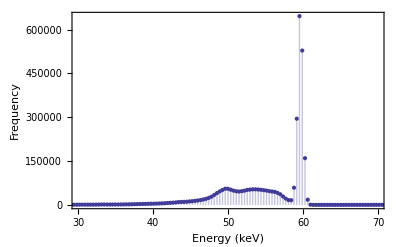

```mathematica
ListPlot[data[1,1][[1;;200,{2,3}]],

ImageSize->imagesize,
Filling->Axis,
PlotTheme->"Classic",
Frame->True,
FrameTicks->{{True,False},{True,False}},
PlotRange->{{30,70},{0,All}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"}
]
Export["../Thesis/Draft/Figures/dataset1zoomed.png",%,ImageResolution->imagedpi];
```

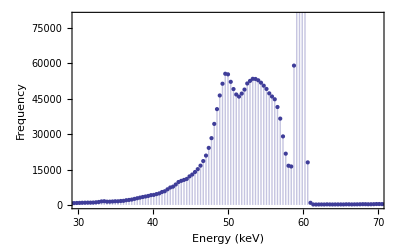

```mathematica
Show[ListPlot[data[1,1][[1;;200,{2,3}]],

ImageSize->imagesize,
Filling->Axis,
PlotTheme->"Classic",
Frame->True,
FrameTicks->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
PlotRange->All,
FrameLabel->{"Energy (keV)","Frequency"}
],
PlotRange->{{30,70},{0,viewingheight[[1]]}}]
Export["../Thesis/Draft/Figures/oldbackground.png",%,ImageResolution->imagedpi];
```

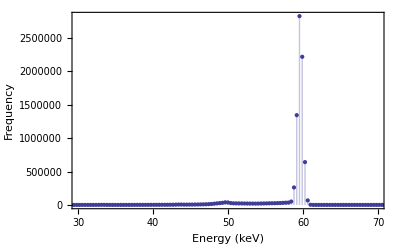

```mathematica
ListPlot[data[4,1][[1;;200,{2,3}]],

ImageSize->imagesize,
Filling->Axis,
PlotTheme->"Classic",
Frame->True,
FrameTicks->{{True,False},{True,False}},
PlotRange->{{30,70},{0,All}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"}
]
Export["../Thesis/Draft/Figures/newdatazoom.png",%,ImageResolution->imagedpi];
```

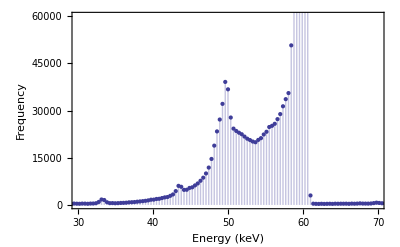

```mathematica
Show[ListPlot[data[4,1][[1;;200,{2,3}]],

ImageSize->imagesize,
Filling->Axis,
PlotTheme->"Classic",
Frame->True,
FrameTicks->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
PlotRange->All,
FrameLabel->{"Energy (keV)","Frequency"}
],
PlotRange->{{30,70},{0,viewingheight[[4]]}}]
Export["../Thesis/Draft/Figures/newbackground.png",%,ImageResolution->imagedpi];
```

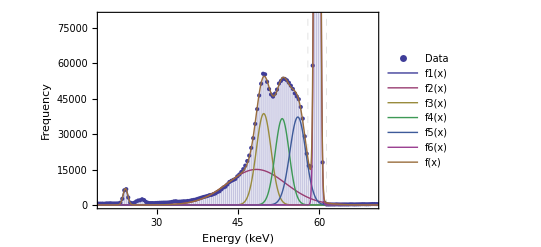

```mathematica
Show[
ListPlot[data[set,k][[region[[set,1]];;region[[set,2]],{2,3}]],
Filling->Bottom,
PlotTheme->theme,
PlotRange->All,
PlotLegends->{"Data"}
],

Plot[Evaluate@Join[Table[F[x,params[set,k][[i]],params[set,k][[i+npeaks[[set]]]],params[set,k][[i+2npeaks[[set]]]]],{i,1,npeaks[[set]]}],{F@@Join[{x},params[set,k][[;;npeaks[[set]]]],params[set,k][[npeaks[[set]]+1;;2npeaks[[set]]]],params[set,k][[2npeaks[[set]]+1;;3npeaks[[set]]]]]}],
{x,-10,200},
PlotLegends->Join[Table["f"<>ToString[i]<>"(x)",{i,npeaks[[set]]}],{"f(x)"}],
PlotRange->All,
PlotTheme->theme],

Frame->{{True,False},{True,False}},
PlotRange->{viewingrange,{0,viewingheight[[set]]}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"zoomed.png",%,ImageResolution->imagedpi];
```

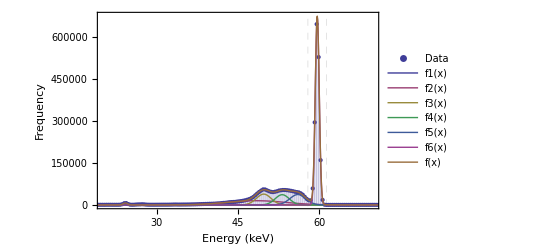

```mathematica
Show[
ListPlot[data[set,k][[region[[set,1]];;region[[set,2]],{2,3}]],
Filling->Bottom,
PlotTheme->theme,
PlotRange->All,
PlotLegends->{"Data"}
],

Plot[Evaluate@Join[Table[F[x,params[set,k][[i]],params[set,k][[i+npeaks[[set]]]],params[set,k][[i+2npeaks[[set]]]]],{i,1,npeaks[[set]]}],{F@@Join[{x},params[set,k][[;;npeaks[[set]]]],params[set,k][[npeaks[[set]]+1;;2npeaks[[set]]]],params[set,k][[2npeaks[[set]]+1;;3npeaks[[set]]]]]}],
{x,-10,200},
PlotLegends->Join[Table["f"<>ToString[i]<>"(x)",{i,npeaks[[set]]}],{"f(x)"}],
PlotRange->All,
PlotTheme->theme],

ImageSize->imagesize,
Frame->{{True,False},{True,False}},
PlotRange->{viewingrange,All},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>".png",%,ImageResolution->imagedpi];
```

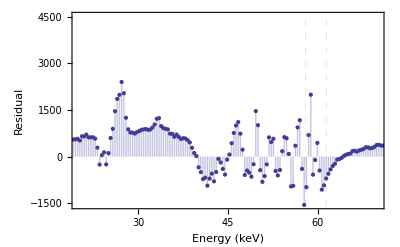

```mathematica
ListPlot[
Join[Table[{energy[set,k][[1]]+energy[set,k][[2]](i-1)},{i,region[[set,1]],region[[set,2]]}],Transpose[{model[set,k]["FitResiduals"]}],2],

ImageSize->imagesize,
Filling->Axis,
Frame->{{True,False},{True,False}},
FrameTicks->{{True,False},{True,False}},
Axes->True,
PlotRange->{viewingrange,All},
PlotTheme->theme,
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Residual"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"residuals.png",%,ImageResolution->imagedpi];
```

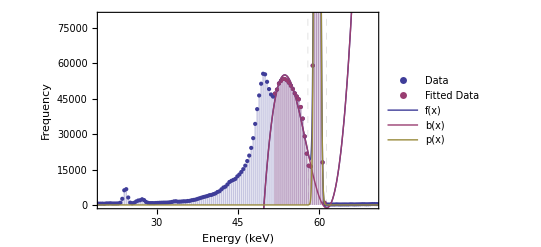

```mathematica
Show[
ListPlot[{data[set,k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[set,k][[cregion[[set,1]];;cregion[[set,2]],{2,3}]]},
Filling->Axis,
PlotRange->All,
PlotTheme->theme,
PlotLegends->{"Data","Fitted Data"}
],

Plot[{cmodel[set,k]["BestFit"],cparams[set,k][[1]]x^3+cparams[set,k][[2]]x^2+cparams[set,k][[3]]x+cparams[set,k][[4]],F[x,cparams[set,k][[-3]],cparams[set,k][[-2]],cparams[set,k][[-1]]]},
{x,-10,100},
PlotTheme->theme,
PlotLegends->{"f(x)","b(x)","p(x)"}
],

ImageSize->imagesize,
PlotRange->{viewingrange,{0,viewingheight[[set]]}},
Frame->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"cubiczoomed.png",%,ImageResolution->imagedpi];
```

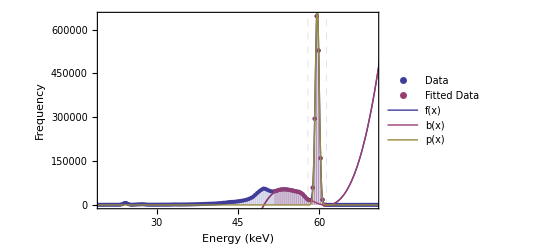

```mathematica
Show[
ListPlot[{data[set,k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[set,k][[cregion[[set,1]];;cregion[[set,2]],{2,3}]]},
Filling->Axis,
PlotRange->All,
PlotTheme->theme,
PlotLegends->{"Data","Fitted Data"}
],

Plot[{cmodel[set,k]["BestFit"],cparams[set,k][[1]]x^3+cparams[set,k][[2]]x^2+cparams[set,k][[3]]x+cparams[set,k][[4]],F[x,cparams[set,k][[-3]],cparams[set,k][[-2]],cparams[set,k][[-1]]]},
{x,-10,100},
PlotTheme->theme,
PlotLegends->{"f(x)","b(x)","p(x)"}
],

ImageSize->imagesize,
PlotRange->{viewingrange,{0,Max[data[set,k][[All,3]]]}},
Frame->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"cubic.png",%,ImageResolution->imagedpi];
```

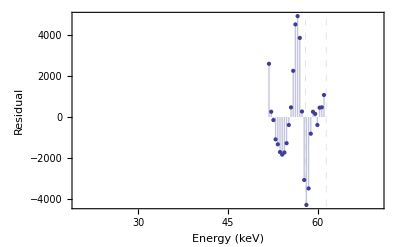

```mathematica
ListPlot[
Join[Table[{energy[set,k][[1]]+energy[set,k][[2]](i-1)},{i,cregion[[set,1]],cregion[[set,2]]}],Transpose[{cmodel[set,k]["FitResiduals"]}],2],

Filling->Axis,
Frame->{{True,False},{True,False}},
FrameTicks->{{True,False},{True,False}},
Axes->True,
PlotRange->{viewingrange,All},
PlotTheme->theme,
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Residual"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"cubicresiduals.png",%,ImageResolution->imagedpi];
```

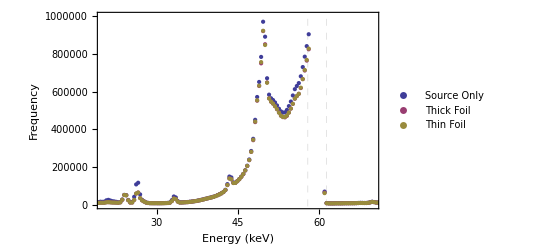

```mathematica
set=5;
Show[
ListPlot[{data[5,1][[;;200,{2,3}]],data[5,3][[;;200,{2,3}]],data[5,4][[;;200,{2,3}]]},
PlotRange->All,
PlotTheme->"Classic",
(*Filling->Axis,*)
PlotLegends->{"Source Only","Thick Foil","Thin Foil"}
],
Frame->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None},
PlotRange->{viewingrange,{0,viewingheight[[set]]}}
]
```

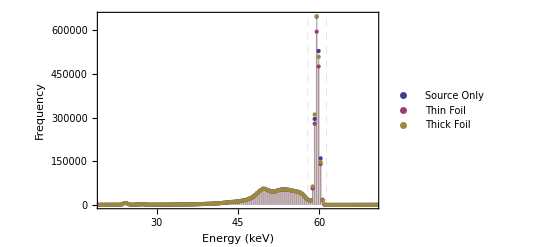

```mathematica
Show[
ListPlot[{data[1,1][[;;200,{2,3}]],data[1,3][[;;200,{2,3}]],data[1,4][[;;200,{2,3}]]},
PlotRange->All,
PlotTheme->"Classic",
Filling->Axis,
PlotLegends->{"Source Only","Thin Foil","Thick Foil"}
],
Frame->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None},
PlotRange->{viewingrange,All}
]
```

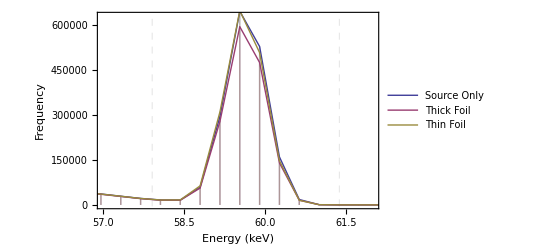

```mathematica
set=1;
Show[
ListPlot[{data[set,1][[;;200,{2,3}]],data[set,3][[;;200,{2,3}]],data[set,4][[;;200,{2,3}]]},
PlotRange->All,
PlotStyle->{PointSize[0]},
Filling->Axis,
PlotTheme->"Classic"
],

ListLinePlot[{data[set,1][[;;200,{2,3}]],data[set,3][[;;200,{2,3}]],data[set,4][[;;200,{2,3}]]},
PlotRange->All,
PlotTheme->"Classic",
PlotLegends->{"Source Only","Thick Foil","Thin Foil"}
],

Frame->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None},
PlotRange->{{57,62},{0,630000}}
]
Export["../Thesis/Draft/Figures/allpeaks.png",%,ImageResolution->imagedpi];
```

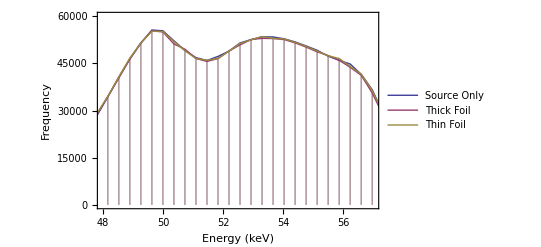

```mathematica
set=1;
Show[
ListPlot[{data[set,1][[;;200,{2,3}]],data[set,3][[;;200,{2,3}]],data[set,4][[;;200,{2,3}]]},
PlotRange->All,
PlotStyle->{PointSize[0]},
Filling->Axis,
PlotTheme->"Classic"
],

ListLinePlot[{data[set,1][[;;200,{2,3}]],data[set,3][[;;200,{2,3}]],data[set,4][[;;200,{2,3}]]},
PlotRange->All,
PlotTheme->"Classic",
PlotLegends->{"Source Only","Thick Foil","Thin Foil"}
],

Frame->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None},
PlotRange->{{48,57},{0,60000}}
]
Export["../Thesis/Draft/Figures/allbackground.png",%,ImageResolution->imagedpi];
```

### Sample Graphs

```mathematica
viewingrange={20,70};
viewingregion={50,200};
theme="Classic";imagesize=Medium;fontsize=13;titlesize=20;
viewingheight={80000,80000,60000,60000,1000000};
imagesize=400;
imagedpi=300;
fontsize=13;
set=4;
k=1;
```

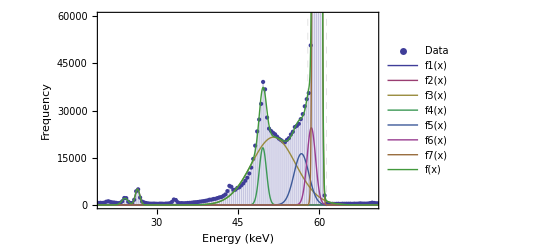

```mathematica
Show[
ListPlot[data[set,k][[region[[set,1]];;region[[set,2]],{2,3}]],
Filling->Bottom,
PlotTheme->theme,
PlotRange->All,
PlotLegends->{"Data"}
],

Plot[Evaluate@Join[Table[F[x,params[set,k][[i]],params[set,k][[i+npeaks[[set]]]],params[set,k][[i+2npeaks[[set]]]]],{i,1,npeaks[[set]]}],{F@@Join[{x},params[set,k][[;;npeaks[[set]]]],params[set,k][[npeaks[[set]]+1;;2npeaks[[set]]]],params[set,k][[2npeaks[[set]]+1;;3npeaks[[set]]]]]}],
{x,-10,200},
PlotLegends->Join[Table["f"<>ToString[i]<>"(x)",{i,npeaks[[set]]}],{"f(x)"}],
PlotRange->All,
PlotTheme->theme],

Frame->{{True,False},{True,False}},
PlotRange->{viewingrange,{0,viewingheight[[set]]}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"zoomed.png",%,ImageResolution->imagedpi];
```

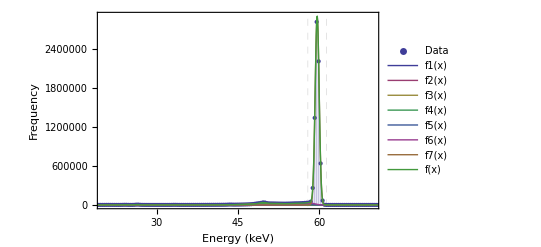

```mathematica
Show[
ListPlot[data[set,k][[region[[set,1]];;region[[set,2]],{2,3}]],
Filling->Bottom,
PlotTheme->theme,
PlotRange->All,
PlotLegends->{"Data"}
],

Plot[Evaluate@Join[Table[F[x,params[set,k][[i]],params[set,k][[i+npeaks[[set]]]],params[set,k][[i+2npeaks[[set]]]]],{i,1,npeaks[[set]]}],{F@@Join[{x},params[set,k][[;;npeaks[[set]]]],params[set,k][[npeaks[[set]]+1;;2npeaks[[set]]]],params[set,k][[2npeaks[[set]]+1;;3npeaks[[set]]]]]}],
{x,-10,200},
PlotLegends->Join[Table["f"<>ToString[i]<>"(x)",{i,npeaks[[set]]}],{"f(x)"}],
PlotRange->All,
PlotTheme->theme],

ImageSize->imagesize,
Frame->{{True,False},{True,False}},
PlotRange->{viewingrange,All},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>".png",%,ImageResolution->imagedpi];
```

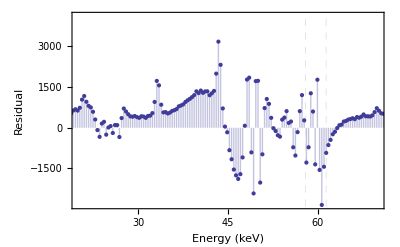

```mathematica
ListPlot[
Join[Table[{energy[set,k][[1]]+energy[set,k][[2]](i-1)},{i,region[[set,1]],region[[set,2]]}],Transpose[{model[set,k]["FitResiduals"]}],2],

ImageSize->imagesize,
Filling->Axis,
Frame->{{True,False},{True,False}},
FrameTicks->{{True,False},{True,False}},
Axes->True,
PlotRange->{viewingrange,All},
PlotTheme->theme,
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Residual"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"residuals.png",%,ImageResolution->imagedpi];
```

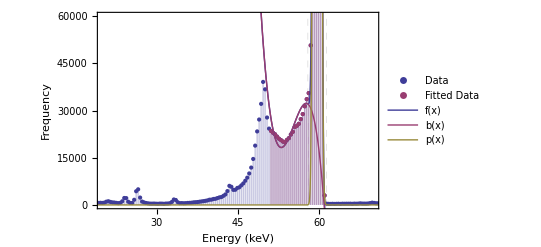

```mathematica
Show[
ListPlot[{data[set,k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[set,k][[cregion[[set,1]];;cregion[[set,2]],{2,3}]]},
Filling->Axis,
PlotRange->All,
PlotTheme->theme,
PlotLegends->{"Data","Fitted Data"}
],

Plot[{cmodel[set,k]["BestFit"],cparams[set,k][[1]]x^3+cparams[set,k][[2]]x^2+cparams[set,k][[3]]x+cparams[set,k][[4]],F[x,cparams[set,k][[-3]],cparams[set,k][[-2]],cparams[set,k][[-1]]]},
{x,-10,100},
PlotTheme->theme,
PlotLegends->{"f(x)","b(x)","p(x)"}
],

ImageSize->imagesize,
PlotRange->{viewingrange,{0,viewingheight[[set]]}},
Frame->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"cubiczoomed.png",%,ImageResolution->imagedpi];
```

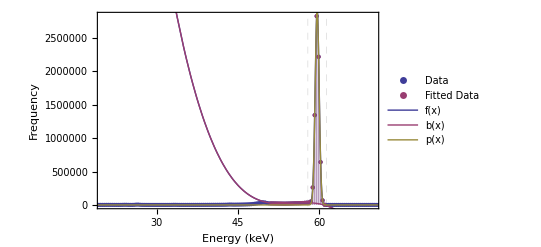

```mathematica
Show[
ListPlot[{data[set,k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[set,k][[cregion[[set,1]];;cregion[[set,2]],{2,3}]]},
Filling->Axis,
PlotRange->All,
PlotTheme->theme,
PlotLegends->{"Data","Fitted Data"}
],

Plot[{cmodel[set,k]["BestFit"],cparams[set,k][[1]]x^3+cparams[set,k][[2]]x^2+cparams[set,k][[3]]x+cparams[set,k][[4]],F[x,cparams[set,k][[-3]],cparams[set,k][[-2]],cparams[set,k][[-1]]]},
{x,-10,100},
PlotTheme->theme,
PlotLegends->{"f(x)","b(x)","p(x)"}
],

ImageSize->imagesize,
PlotRange->{viewingrange,{0,Max[data[set,k][[All,3]]]}},
Frame->{{True,False},{True,False}},
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Frequency"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"cubic.png",%,ImageResolution->imagedpi];
```

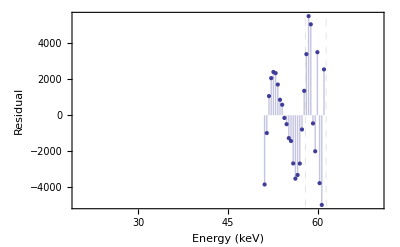

```mathematica
ListPlot[
Join[Table[{energy[set,k][[1]]+energy[set,k][[2]](i-1)},{i,cregion[[set,1]],cregion[[set,2]]}],Transpose[{cmodel[set,k]["FitResiduals"]}],2],

Filling->Axis,
Frame->{{True,False},{True,False}},
FrameTicks->{{True,False},{True,False}},
Axes->True,
PlotRange->{viewingrange,All},
PlotTheme->theme,
ImageSize->imagesize,
BaseStyle->{FontSize->fontsize},
FrameLabel->{"Energy (keV)","Residual"},
GridLines->{{{params[set,k][[npeaks[[set]]]]-2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]},{params[set,k][[npeaks[[set]]]]+2*fwhm[params[set,k][[2npeaks[[set]]]]],Directive[Dashed]}},None}
]
Export["../Thesis/Draft/Figures/modelset"<>ToString[set]<>"trial"<>ToString[k]<>"cubicresiduals.png",%,ImageResolution->imagedpi];
```